# Hessenberg both ways

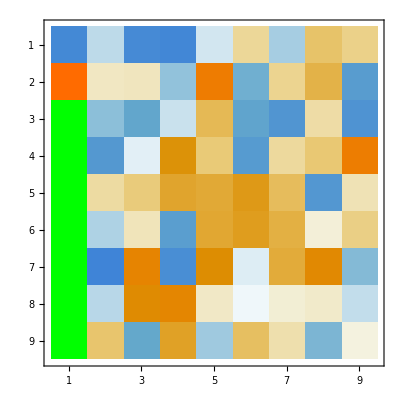
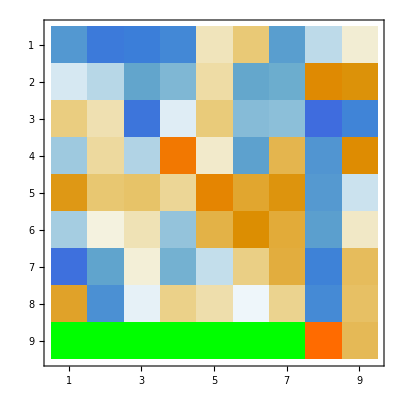

```mathematica
m=9;
A=RandomReal[{-1,1},{m,m}];
v=u=ConstantArray[0,m];
v⟦2;;m⟧=A⟦2;;m,1⟧; (* bottom of first column*)
u⟦1;;m-1⟧=A⟦m,1;;m-1⟧; (* left side of last row *)
u⟦m-1⟧-=Norm[u];
v⟦2⟧-=Norm[v];
{u,v}=Map[Normalize,{u,v}];
QV=IdentityMatrix[m]-2 KroneckerProduct[v,v];
QU=IdentityMatrix[m]-2 KroneckerProduct[u,u];
Map[MatrixPlot[Chop[#.A.#ᵀ],ColorRules->{0->Green}]&,{QV,QU}]
```

# Bulge To Spike

If you decompose the inner portion (leaving a margin of one) then you can maintain the same overall foot print of the bulge. See “3” below.

```mathematica
{m,b,s}={34,23,8};
SetOptions[MatrixPlot,MeshStyle->Thick,ColorRules->{0->LightGreen}];
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
A=Chop[HessenbergDecomposition[A]⟦2⟧];
Bulge=RandomReal[{-1,1},{b,b}];
Bulge=Bulge+Bulgeᵀ;
A[[s+1;;s+b,s+1;;s+b]]=Bulge;
InnerBulge=Bulge[[2;;-2,2;;-2]];
{Q1Sub,Q2Sub}=Map[
SchurDecomposition[#]⟦1⟧&,{Bulge,InnerBulge}];
Q1=Q2=SparseArray[Band[{1,1}]->1.0,{m,m}];
Q1[[s+1;;s+b,s+1;;s+b]]=Q1Sub;
Q2[[s+2;;s+b-1,s+2;;s+b-1]]=Q2Sub;
mesh={s-1,s,s+1,s+b-1,s+b,s+b+1};
TabView[Map[
MatrixPlot[#,
Mesh->{mesh,mesh}]&,
{A,Chop[Q1ᵀ.A.Q1],Chop[Q2ᵀ.A.Q2]}],3]
```

123

I am going to maintain the footprint. To get back I can do a single “Hessenberg step” on both sides. I am going to look at the ordering of the spikes.

```mathematica
{m,b,s}={34,23,8};
A=RandomReal[{-1,1},{m,m}];A=Chop[HessenbergDecomposition[A+Aᵀ]⟦2⟧];
Bulge=RandomReal[{-1,1},{b,b}];Bulge=Bulge+Bulgeᵀ;
A[[s+1;;s+b,s+1;;s+b]]=Bulge;
InnerBulge=Bulge[[2;;-2,2;;-2]];
Q1=SparseArray[Band[{1,1}]->1.0,{m,m}];
Q1[[s+2;;s+b-1,s+2;;s+b-1]]=SchurDecomposition[InnerBulge]⟦1⟧;
mesh={s,s+1,s+b-1,s+b};
TabView[Map[
MatrixPlot[#,
Mesh->{mesh,mesh}]&,
{A,Chop[Spike=Q1ᵀ.A.Q1]}],2];
TabView[{"all"->ListPlot[
{Abs[Spike⟦All,s+1⟧],Abs[Spike⟦All,s+b⟧],Abs[Spike⟦s+1,All⟧]+1,Abs[Spike⟦s+b,All⟧]+1},
Joined->True,
PlotRange->All],
"spike"->ListLogPlot[{Abs[Spike⟦s;;s+b,s+1⟧],Abs[Spike⟦s+b,s+1;;s+b+1⟧]},
Joined->True,GridLines->Automatic,
PlotRange->All]},2]
```

12

Turning on pivoting  does not do what I hoped it would do.

```mathematica
{m,b,s}={34,23,8};
A=RandomReal[{-1,1},{m,m}];A=Chop[HessenbergDecomposition[A+Aᵀ]⟦2⟧];
Bulge=RandomReal[{-1,1},{b,b}];Bulge=Bulge+Bulgeᵀ;
A[[s+1;;s+b,s+1;;s+b]]=Bulge;
InnerBulge=Bulge[[2;;-2,2;;-2]];
Q1=SparseArray[Band[{1,1}]->1.0,{m,m}];
{Q1[[s+2;;s+b-1,s+2;;s+b-1]],T,d}=SchurDecomposition[InnerBulge,Pivoting->True];
mesh={s,s+1,s+b-1,s+b};
TabView[Map[
MatrixPlot[#,
Mesh->{mesh,mesh}]&,
{A,Chop[Spike=Q1ᵀ.A.Q1]}],2]
TabView[{"all"->ListPlot[
{Abs[Spike⟦All,s+1⟧],Abs[Spike⟦All,s+b⟧],Abs[Spike⟦s+1,All⟧]+1,Abs[Spike⟦s+b,All⟧]+1},
Joined->True,
PlotRange->All],
"spike"->ListLogPlot[{Abs[Spike⟦s;;s+b,s+1⟧],Abs[Spike⟦s+b,s+1;;s+b+1⟧]},
Joined->True,GridLines->Automatic,
PlotRange->All]},2]
```

12

12

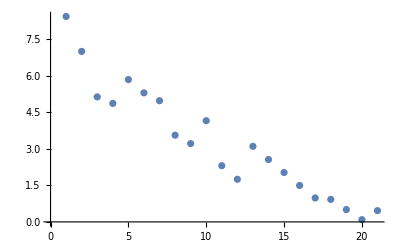

```mathematica
{Q1[[s+2;;s+b-1,s+2;;s+b-1]],T,d}=SchurDecomposition[InnerBulge,Pivoting->True,RealBlockDiagonalForm->False];
ListPlot[Abs[Diagonal[T]]]
```

What I really want to do is order the spikes

```mathematica
{m,b,s}={34,23,8};
A=RandomReal[{-1,1},{m,m}];A=Chop[HessenbergDecomposition[A+Aᵀ]⟦2⟧];
Bulge=RandomReal[{-1,1},{b,b}];Bulge=Bulge+Bulgeᵀ;
A[[s+1;;s+b,s+1;;s+b]]=Bulge;
InnerBulge=Bulge[[2;;-2,2;;-2]];
Q1=SparseArray[Band[{1,1}]->1.0,{m,m}];
{Q1[[s+2;;s+b-1,s+2;;s+b-1]],T,d}=SchurDecomposition[InnerBulge,Pivoting->True];
mesh={s,s+1,s+b-1,s+b};
TabView[Map[
MatrixPlot[#,
Mesh->{mesh,mesh}]&,
{A,Chop[Spike=Q1ᵀ.A.Q1]}],2]
TabView[{"all"->ListPlot[
{Abs[Spike⟦All,s+1⟧],Abs[Spike⟦All,s+b⟧],Abs[Spike⟦s+1,All⟧]+1,Abs[Spike⟦s+b,All⟧]+1},
Joined->True,
PlotRange->All],
"spike"->ListLogPlot[{Abs[Spike⟦s;;s+b,s+1⟧],Abs[Spike⟦s+b,s+1;;s+b+1⟧]},
Joined->True,GridLines->Automatic,
PlotRange->All]},2]
```

```mathematica
Apply[Times,Spike⟦s;;s+b,s+1⟧]
Apply[Times,Spike⟦s+b,s+1;;s+b+1⟧]
```

-2.78696×10^-10

-1.9218×10^-10

## Delay ODE in Mma

The Mma solvers are pretty robust and simple to use.

quick Literature search shows some recent DDE solver pubs
Eur. Phys. J. Plus (2017) 132: 51 THE EUROPEAN
PHYSICAL JOURNAL PLUS
A new efficient method for solving delay differential equations
and a comparison with other methods
Necdet Bildika and Sinan Denizb

A Mma tutorial
https://reference.wolfram.com/language/tutorial/NDSolveDelayDifferentialEquations.html

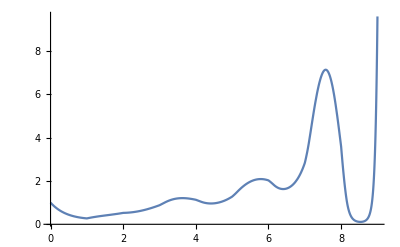

```mathematica
TMax=9;
xSol=NDSolveValue[{
x'[t]==x[t](x[t-Pi]-x'[t-1]),
x[t/;t≤0]==Cos[t]
},x,{t,0,TMax}];
Plot[xSol[t],{t,0, TMax},PlotRange->All]
```

```mathematica
?NDSolveValue
```

## 1D Manifolds and DDE

For an autonomous discrete dynamical system 
	y_(n+1)=F(y_n)
with a hyperbolic fixed point 
	p=F(p)
Here hyperbolic means that 
	DF(p)
has no eigenvalues on the unit circle.  The interpretation is that eigenvalues less than one in magnitude shrink things while eigenvalues larger than one in absolute value expand things.  Eigenvalues of size one do not classify behavior. 

If all the eigenvalues are less than one everything shrinks down onto the fixed point and it is called stable. If all the eigenvalues are bigger than one then everything expands.  Clearly this is called unstable.  Even if only one eigenvalue is bigger than one then p is still unstable: in practice there will always be some small non-zero component in the eigen direction of the “big” eigenvector and exponential growth will rapidly make that component dominate.  

The stable manifold is all the stuff that gets sucked into a hyperbolic fixed point.  Near the fixed point it aligns with the appropriate set of eigen vectors.    	

The unstable manifold is all the stuff that gets spat out of the hyperbolic fixed point. 

Lots of literature makes a distinction between local and global manifolds. They may well have slightly divergent (in detail) definitions.  The entire manifolds are very complicated.

The aim is to build a solver based on moderately standard DDE solvers.  The key observation is that a 1D invariant manifold  satisfies 
	y(s)=F(y(s-1))
which if you differentiate is 
	y'(s)=DF(y(s-1)).y'(s-1)
which starts to look vaguely like a delay ODE.